```mathematica
Needs["GraphUtilities`"]
```

## Substitution and Evaluation

This Mathematica notebook is licensed under a  
It creates the demonstrations used in the post 

I hope anyone interested will feel free to improve this work and to use it in their own publications and coursework.

Second notebook in a series; first was Substitution in algebra.nb.

This notebook contains the coding needed to produce the diagrams in the post The only axiom of algebra.

### Basic definitions

Based on experimental work done in New Algebra.nb and Show binops exp 2014 0321.nb

```mathematica
makelabel[labs_,n_]:=Inset/@#/.labs&[n]
```

```mathematica
vertexstyle[n_]:=Framed[Style[n,FontFamily->"Arial",FontColor->Black,FontSize->12],Background->White,FrameMargins->{{3,3},{3,3}}]
```

```mathematica
vertexstyle[42]
```

42

```mathematica
edgelabelstyle[n_]:=Style[Framed[n,Background->White,FrameMargins->{{0,0},{0,0}},FrameStyle->White],Plain,FontFamily->"Arial"]
```

```mathematica
edgelabelstyle[42]
```

42

```mathematica
vrf1[labs_]:=
VertexRenderingFunction->({White,EdgeForm[Black],Black,Text[vertexstyle[makelabel[labs, #2]],#1]}&)
```

```mathematica
erf1=EdgeRenderingFunction->({Darker[Red],{Line[#1]},Text[If[#3===None,Null,edgelabelstyle[#3]],Total[#1]/2.]}&)
```

EdgeRenderingFunction→({Darker[Red],{Line[#1]},Text[If[#3===None,Null,edgelabelstyle[#3]],Total[#1]/2.]}&)

```mathematica
stree[skel_,labs_,vfr_,erf_,vcr_,imagesize_,asprat_]:=GraphPlot[skel,vfr[labs], erf,VertexCoordinateRules->vcr,EdgeLabeling->True,ImageSize->imagesize,AspectRatio ->asprat]
```

```mathematica
emptybox="  "
```

### Associative law building blocks

```mathematica
lassoc=GraphPlot[{1->2,2->3,2->4,1->5},{1->"Δ",2->"Δ",3->"a",4->"b",5->"c"}//vrf1,VertexCoordinateRules->{1->{1,1},2->{0,0},3->{-.67,-1},4->{.67,-1},5->{2,-1}},
ImageSize->100,AspectRatio->1]
```

-Graphics-

```mathematica
raggedlassoc=GraphPlot[{1->2,1->3,2->4,2->5},{1->"Δ",2->"Δ",3->"c",4->"a",5->"b"}//vrf1,VertexCoordinateRules->{1->{1,1},2->{0,0},3->{2,0},4->{-.67,-1},5->{.67,-1}},
ImageSize->100,AspectRatio->1]
```

-Graphics-

```mathematica
rassoc=GraphPlot[{1->2,1->3,2->4,2->5},{1->"Δ",2->"Δ",3->"a",4->"b",5->"c"}//vrf1,VertexCoordinateRules->{1->{1,1},2->{1.5,0},3->{-.67,-1},4->{.67,-1},5->{2,-1}},
ImageSize->100,AspectRatio->1]
```

-Graphics-

```mathematica
minusex=GraphPlot[{1->2,1->3,2->4,2->5},{1->"minus",2->"minus",3->"c",4->"a",5->"b"}//vrf1,VertexCoordinateRules->{1->{1,1},2->{0,0},3->{2,0},4->{-.67,-1},5->{.67,-1}},
ImageSize->120,AspectRatio->1]
```

-Graphics-

## Only axiom

```mathematica
commutestage1b=GraphPlot[{1->2,1->3},{1->"+",2->emptybox,3->"5"}//vrf1,VertexCoordinateRules->{1->{1,1},2->{0,-1},3->{2,-1}},
ImageSize->70,AspectRatio->1.2]
```

-Graphics-

```mathematica
altcommutestage1b=GraphPlot[{1->2,1->3},{1->"+",2->emptybox,3->emptybox}//vrf1,VertexCoordinateRules->{1->{1,1},2->{0,-1},3->{2,-1}},
ImageSize->70,AspectRatio->1.2]
```

-Graphics-

```mathematica
commutestage1a=GraphPlot[{1->2,1->3},{1->"×",2->"3",3->"4"}//vrf1,VertexCoordinateRules->{1->{1,1},2->{0,-1},3->{2,-1}},
ImageSize->70,AspectRatio->1.2]
```

-Graphics-

```mathematica
commutestage2=GraphPlot[{1->2,2->3,2->4,1->5},{1->"+",2->"×",3->"3",4->"4",5->"5"}//vrf1,VertexCoordinateRules->{1->{1,1},2->{0,0},3->{-.67,-1},4->{.67,-1},5->{2,0}},
ImageSize->110,AspectRatio->1.4]
```

-Graphics-

```mathematica
altcommutestage2=GraphPlot[{1->2,2->3,2->4,1->5},{1->"+",2->"×",3->emptybox,4->emptybox,5->emptybox}//vrf1,VertexCoordinateRules->{1->{1,1},2->{0,0},3->{-.67,-1},4->{.67,-1},5->{2,0}},
ImageSize->110,AspectRatio->1.4]
```

-Graphics-

```mathematica
diffcommutestage2b=GraphPlot[{1->2,2->3,2->4,1->5},{1->"+",2->"×",3->"3",4->"4",5->emptybox}//vrf1,VertexCoordinateRules->{1->{1,1},2->{0,0},3->{-.67,-1},4->{.67,-1},5->{2,0}},
ImageSize->110,AspectRatio->1.4]
```

-Graphics-

```mathematica
raltcommutestage2bis=GraphPlot[{1->2,5->3,5->4,1->5},{1->"+",5->"×",3->"3",4->"4",2->"12"}//vrf1,VertexCoordinateRules->{1->{1,1},2->{0,0},3->{1.33,-1},4->{2.67,-1},5->{2,0}},
ImageSize->110,AspectRatio->1.4]
```

-Graphics-

```mathematica
commutestage4=GraphPlot[{1->2,1->3},{1->"+",2->"12",3->"5"}//vrf1,VertexCoordinateRules->{1->{1,1},2->{0,-1},3->{2,-1}},
ImageSize->70,AspectRatio->1.2]
```

-Graphics-

```mathematica
altcommutestage4=GraphPlot[{1->2,1->3},{1->"+",2->"12",3->emptybox}//vrf1,VertexCoordinateRules->{1->{1,1},2->{0,-1},3->{2,-1}},
ImageSize->70,AspectRatio->1.2]
```

-Graphics-

```mathematica
commutestage2a=Show[Graphics[{Inset[vertexstyle[12],{0,0}]}],ImageMargins->1,ImageSize->40]
```

-Graphics-

```mathematica
commutestage6=Show[Graphics[{Inset[vertexstyle[17],{0,0}]}],ImageMargins->1,ImageSize->40]
```

-Graphics-

```mathematica
curvarr=Show[Graphics[{Arrowheads->.2,Arrow[BezierCurve[{{0,0},{1,-1},{2,.9}}]]}],ImageSize->50]
```

-Graphics-

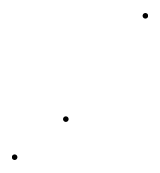

```mathematica
commutestage1=Show[Graphics[{Arrowheads->100,Inset[commutestage1a,{1,0}],Inset[curvarr,{1.47,.35}],Inset[commutestage1b,{2.2,1.3}]}],ImageSize->160]
```

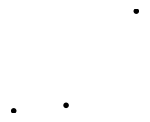

```mathematica
commutestage3=Show[Graphics[{Arrowheads->100,Inset[commutestage2a,{1,.3}],Inset[curvarr,{1.47,.35}],Inset[commutestage1b,{2.1,1.2}]}],ImageSize->150]
```

```mathematica
diffcommutestage1=Show[Graphics[{Arrowheads->100,Inset[commutestage1a,{1,0}],Inset[curvarr,{1.47,.35}],Inset[altcommutestage1b,{2.2,1.3}]}],ImageSize->160]
```

-Graphics-

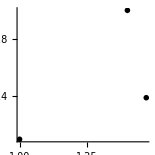

```mathematica
rcommutestage1=Show[Graphics[{Arrowheads->100,Inset[commutestage1a,{1,0.1}],Inset[curvarr,{1.47,.39}],Inset[altcommutestage4,{1.4,1}]}],AspectRatio->1,ImageSize->155,Axes->True,AxesStyle->Directive[Transparent,12],AxesOrigin->{0,0}]
```

```mathematica
Framed[1/x+y+z,Background->White]
```

1/x+y+z

```mathematica
myframe=Framed[#,Background->White]&
```

#1&

```mathematica
myblue=Darker[Blue]
```

RGBColor[0,0,2/3]

```mathematica
commdiag1=Graphics[{Arrowheads[.02],myblue,Thick,
Arrow[{{0,0},{5,2.5}},{1.75,1.25}],
Inset[Style["substitute",13,FontFamily->"Arial"]//myframe,{2.5+.2,1.25+.1}],
Arrow[{{0,0},{5,-2.5}},{1.75,1.75}],
Inset[Style["eval,id",13,FontFamily->"Arial"]//myframe,{2.5-.15,-1.25-.075}],
Arrow[{{5,2.5},{9.5,0}},{1.4,.9}],
Inset[Style["eval",13,FontFamily->"Arial"]//myframe,{7.4,1.175}],
Arrow[{{5,-4},{9.5,0}},{2,1}],
Inset[Style["substitute",13,FontFamily->"Arial"]//myframe,{5+2.7,0-1.75}],
Inset[commutestage1//Framed,{0,0}],Inset[commutestage2//Framed,{5,2}],Inset[commutestage3//Framed,{5,-2.5}],Inset[commutestage4//Framed,{9.5,0}]},ImageSize->650]
```

-Graphics-